# Quick overview of common gates

## Key Concepts

Matrix multiplication

Tensor product

Unitary matrix

## Single qubit gates

Quantum circuits are usually represented using conventional names for the corresponding gates. For example, consider the circuit below:

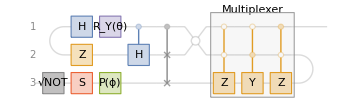

```mathematica
ClearAll[θ,ϕ];
QuantumCircuitOperator[{"Cup","H","Z"->2,"RY"[θ],"RootNOT"->3,"S"->3,"P"[ϕ]->3,"CH","CSWAP","ZSpider"->{1,2}->{1,2},"Multiplexer"["Z","Y","Z"],"Cap"->{2,3}}]["Diagram"]
```

The notations and symbols provided are usually sufficient to construct the corresponding operators and perform the calculations. Next, we will discuss some common gates and elaborate on their effects on the quantum state.

### Pauli gates

Pauli operators are a common set of single-qubit gates. The Pauli-Z operator acts like a phase flip: it leaves the 0 state unchanged and adds a minus sign to the 1 state. In other words, if a qubit has some amount of 0 plus some amount of 1, applying Z keeps the 0 part the same and flips the sign of the 1 part. (By comparison, X swaps the 0 and 1 states, and Y also swaps them but introduces a phase.)

```mathematica
QuantumCircuitOperator["Z"]["CircuitDiagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

Effect of Pauli-Z on the state vector:

```mathematica
ClearAll[α,β];
MatrixForm[{α,β}]->MatrixForm[PauliMatrix[3].{α,β}]
```

(α
β)→(α
-β)

Effect of Pauli-Z in the Dirac notation:

```mathematica
TraditionalForm[QuantumState[{α,β}]]->TraditionalForm[QuantumOperator["Z"]@QuantumState[{α,β}]]
```

α0+β1→α0-β1

The Pauli-Z gate is equivalent to a phase rotation by an angle of pi. Aside from an overall global factor (a “global phase” that doesn’t affect measurement outcomes), they act the same on any qubit: the 0 part is unchanged, and the 1 part picks up a minus sign.

```mathematica
QuantumCircuitOperator["P"]["CircuitDiagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

Effect of Phase-π gate in the Dirac notation :

```mathematica
TraditionalForm[QuantumState[{α,β}]]->TraditionalForm[QuantumOperator["P"]@QuantumState[{α,β}]]
```

α0+β1→α0-β1

Additionally, Pauli-Z operator can be seen as flipping eigenstates of Pauli-X

The Pauli-Z gate turns the plus state (the equal mix of 0 and 1 with the same sign) into the minus state (the equal mix of 0 and 1 with opposite signs)

```mathematica
QuantumState["+"]->QuantumOperator["Z"][QuantumState["+"]]//TraditionalForm
```

1/(√2)0+1/(√2)1→1/(√2)0-1/(√2)1

Check that applying the Pauli-Z gate to the plus state returns the minus state.

```mathematica
QuantumOperator["Z"][QuantumState["+"]]==QuantumState["-"]
```

True

The Pauli-Z gate turns the minus state (equal mix of 0 and 1 with opposite signs) into the plus state (equal mix with the same sign).

```mathematica
QuantumState["-"]->QuantumOperator["Z"][QuantumState["-"]]//TraditionalForm
```

1/(√2)0-1/(√2)1→1/(√2)0+1/(√2)1

Check that applying the Pauli-Z gate to the minus state returns the plus state.

```mathematica
QuantumOperator["Z"][QuantumState["-"]]==QuantumState["+"]
```

True

Let’s visualize the effect of the Pauli-Z gate on different states by comparing the Bloch vectors of the initial and final states.

```mathematica
GraphicsGrid[With[{st=QuantumState[#],op=QuantumOperator["Z"]},{st["BlochPlot"],QuantumCircuitOperator[op]["Diagram","WireLabels"->None],op[st]["BlochPlot"]}]&/@{"+","-","R","L"},Frame->{None,All}]
```

-Graphics-

Pauli-X is also called the “NOT” operator because it acts like a NOT gate on the computational basis.

```mathematica
QuantumCircuitOperator[{"0","X"}]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

Check that applying Pauli-X to the 0 state yields the 1 state.

```mathematica
QuantumCircuitOperator[{"0","X"}][]==QuantumState["1"]
```

True

Check that applying Pauli - X to the 1 state yields the 0 state .

```mathematica
QuantumCircuitOperator[{"1","X"}]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

```mathematica
QuantumCircuitOperator[{"1","X"}][]==QuantumState["0"]
```

True

Let' s visualize the effect of the Pauli - X gate on different states by comparing the Bloch vectors of the initial and final states .

```mathematica
GraphicsGrid[With[{st=QuantumState[#],op=QuantumOperator["X"]},{st["BlochPlot"],QuantumCircuitOperator[op]["Diagram","WireLabels"->None],op[st]["BlochPlot"]}]&/@{"0","1","R","L"},Frame->{None,All}]
```

-Graphics-

Pauli-Y on the 0 state acts like a phase-sensitive flip: it turns 0 into 1, up to an overall phase.

```mathematica
QuantumCircuitOperator[{"0","Y"}]["Diagram","WireLabels"->None,ImageSize->100]
QuantumCircuitOperator[{"0","Y"}][]//TraditionalForm
```

-Graphics-

ⅈ1

Similarly, Pauli-Y on the 1 state acts like a phase-sensitive flip: it turns 0 into 1, up to an overall phase.

```mathematica
QuantumCircuitOperator[{"1","Y"}]["Diagram","WireLabels"->None,ImageSize->100]
QuantumCircuitOperator[{"1","Y"}][]//TraditionalForm
```

-Graphics-

-ⅈ0

Let' s visualize the effect of the Pauli - Y gate on different states by comparing the Bloch vectors of the initial and final states. Note that for the computational basis, the overall phase is not observable.

```mathematica
GraphicsGrid[With[{st=QuantumState[#],op=QuantumOperator["Y"]},{st["BlochPlot"],QuantumCircuitOperator[op]["Diagram","WireLabels"->None],op[st]["BlochPlot"]}]&/@{"0","1","+","-"},Frame->{None,All}]
```

-Graphics-

### Hadamard gate

Another important single-qubit gate is the Hadamard gate.

```mathematica
QuantumCircuitOperator["H"]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

This gate transforms a register state into a uniform superposition state.

```mathematica
QuantumOperator["H"][]//TraditionalForm
```

1/(√2)0+1/(√2)1

Check the result is truly a uniform superposition:

```mathematica
QuantumOperator["H"][]==QuantumState["UniformSuperposition"]
```

True

Show the effect of H-gate on a generic quantum state:

```mathematica
QuantumState[{α,β}]->QuantumOperator["H"][QuantumState[{α,β}]]//TraditionalForm
```

α0+β1→(α/(√2)+β/(√2))0+(α/(√2)-β/(√2))1

Show matrix form of H-gate:

```mathematica
QuantumOperator["H"]["Matrix"]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

### Family of phase-like gates

The phase gate is another important single-qubit gate.

```mathematica
ClearAll[θ];
QuantumCircuitOperator["P"[θ]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

It introduces a phase on the 1 state.

```mathematica
QuantumState[{α,β}]->QuantumOperator["P"[θ]][QuantumState[{α,β}]]//TraditionalForm
```

α0+β1→α0+ⅇ^(ⅈ θ) β1

Show the matrix form of phase gate:

```mathematica
QuantumOperator["P"[θ]]["Matrix"]//MatrixForm
```

(1 | 0
0 | ⅇ^(ⅈ θ))

The S gate is another important single-qubit gate.

```mathematica
QuantumCircuitOperator["S"]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

It introduces a phase on the 1 state.

```mathematica
QuantumState[{α,β}]->QuantumOperator["S"][QuantumState[{α,β}]]//TraditionalForm
```

α0+β1→α0+ⅈ β1

Show matric form of S-gate:

```mathematica
QuantumOperator["S"]["Matrix"]//MatrixForm
```

(1 | 0
0 | ⅈ)

S gate is the same as phase-π/2 gate:

```mathematica
QuantumOperator["S"]==QuantumOperator["P"[π/2]]
```

True

The T gate is another common single-qubit gate.

```mathematica
QuantumCircuitOperator["T"]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

It also introduce a phase on the 1 state.

```mathematica
QuantumState[{α,β}]->QuantumOperator["T"][QuantumState[{α,β}]]//TraditionalForm
```

α0+β1→α0+ⅇ^((ⅈ π)/4) β1

Show matrix forma of T gate:

```mathematica
QuantumOperator["T"]["Matrix"]//MatrixForm
```

(1 | 0
0 | ⅇ^((ⅈ π)/4))

T gate is the same as phase - π/4 gate :

```mathematica
QuantumOperator["T"]==QuantumOperator["P"[π/4]]
```

True

Phase-shift operator is a phase operator with an angle 2π/2^n=π/2^(n-1):

```mathematica
n=5;
QuantumCircuitOperator["PhaseShift"[n]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

The label for the gate is obtained as follows:

```mathematica
1/2^(n-1)
```

1/16

Show that the phase shift is similar to a phase operator:

```mathematica
QuantumOperator["PhaseShift"[n]]==QuantumOperator["P"[π/2^(n-1)]]
```

True

A special case of adding a phase is adding a global phase. This is what we usually call a global phase gate.

```mathematica
ClearAll[θ];
QuantumCircuitOperator["GlobalPhase"[θ]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

Since the phase is global (the same factor in front of all terms in the linear combination), it is not observable—it does not change the physical state.

```mathematica
With[{st=QuantumState["RandomPure"]},st==QuantumOperator["GlobalPhase"[RandomReal[{0,2π}]]][st]]
```

True

### Family of rotation gates

Another important family of single-qubit gates is the set of rotation gates: R_X, R_Y and R_Z that can be understand as rotations around the corresponding x, y, or z axis on the Bloch sphere by a given angle.

Rotation around x-axis:

```mathematica
ClearAll[θ]
QuantumCircuitOperator["RX"[θ]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

R_X[θ]=ⅇ^(-ⅈ θ/2 X)

```mathematica
QuantumOperator["RX"[θ]]==Exp[-ⅈ θ/2 QuantumOperator["X"]]//FullSimplify
```

True

Show the effect of X-rotation on a generic quantum state:

```mathematica
QuantumState[{α,β}]->QuantumOperator["RX"[θ]][QuantumState[{α,β}]]//TraditionalForm
```

α0+β1→(α cos(θ/2)-ⅈ β sin(θ/2))0+(β cos(θ/2)-ⅈ α sin(θ/2))1

Show the matrix form of x-rotation:

```mathematica
QuantumOperator["RX"[θ]]["Matrix"]//MatrixForm
```

(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2])

As mentioned before, an x-rotation is a rotation around the x-axis on the Bloch sphere.

```mathematica
Manipulate[QuantumCircuitOperator["RX"[θ]][]["BlochPlot",ImageSize->200],{{θ,0,"θ in R_X[θ]"},0,2π,AppearanceElements->All}]
```

Rotation around y-axis:

```mathematica
ClearAll[θ]
QuantumCircuitOperator["RY"[θ]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

R_Y[θ]=ⅇ^(-ⅈ θ/2 Y)

```mathematica
QuantumOperator["RY"[θ]]==Exp[-ⅈ θ/2 QuantumOperator["Y"]]//FullSimplify
```

True

Show the effect of y-rotation on a generic quantum state:

```mathematica
QuantumState[{α,β}]->QuantumOperator["RY"[θ]][QuantumState[{α,β}]]//TraditionalForm
```

α0+β1→(α cos(θ/2)-β sin(θ/2))0+(β cos(θ/2)+α sin(θ/2))1

Show the matrix form of y-rotation:

```mathematica
QuantumOperator["RY"[θ]]["Matrix"]//MatrixForm
```

(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2])

As mentioned before, an y-rotation is a rotation around the y-axis on the Bloch sphere.

```mathematica
Manipulate[QuantumCircuitOperator["RY"[θ]][]["BlochPlot",ImageSize->200],{{θ,0,"θ in R_Y[θ]"},0,2π,AppearanceElements->All}]
```

Rotation around z-axis:

```mathematica
QuantumCircuitOperator["RZ"[θ]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

R_Z[θ]=ⅇ^(-ⅈ θ/2 Z)

```mathematica
QuantumOperator["RZ"[θ]]==Exp[-ⅈ θ/2 QuantumOperator["Z"]]//FullSimplify
```

True

Show the effect of z-rotation on a generic quantum state:

```mathematica
QuantumState[{α,β}]->QuantumOperator["RZ"[θ]][QuantumState[{α,β}]]//TraditionalForm
```

α0+β1→ⅇ^(-(ⅈ θ)/2) α0+ⅇ^((ⅈ θ)/2) β1

Show the matrix form of x-rotation:

```mathematica
QuantumOperator["RZ"[θ]]["Matrix"]//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

As mentioned before, an z-rotation is a rotation around the z-axis on the Bloch sphere.

```mathematica
Manipulate[QuantumCircuitOperator["RZ"[θ]][QuantumState["+"]]["BlochPlot",ImageSize->200],{{θ,0,"θ in R_Z[θ]"},0,2π,AppearanceElements->All}]
```

The U3 gate is a general single-qubit rotation formed by combining the earlier rotations. It is defined by three angles.

```mathematica
ClearAll[θ, ϕ ,λ];
QuantumCircuitOperator["U3"[θ, ϕ ,λ]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

Show the matrix forma of U3:

```mathematica
MatrixForm[QuantumOperator["U3"[θ, ϕ ,λ]]["Matrix"]]
```

(Cos[θ/2] | -ⅇ^(ⅈ λ) Sin[θ/2]
ⅇ^(ⅈ ϕ) Sin[θ/2] | ⅇ^(ⅈ (λ+ϕ)) Cos[θ/2])

In the Bloch sphere, the action of U3[λ,θ,ϕ] is the same as EulerMatrix[{θ,λ,ϕ}], which is the Euler 3D rotation matrix formed by rotating by θ around the current z axis, then by λ around the current y axis, and then by ϕ around the current z axis.

For example, generate three random angles, and a point on the Bloch sphere:

```mathematica
ClearAll[λ,θ,ϕ,vec];
{λ,θ,ϕ}=RandomReal[{0,2π},3];
vec=RandomPoint[Sphere[]];
```

Visualize the 3D point and its corresponding Bloch vector:

```mathematica
SymmetricDifference
```

```mathematica
Show[QuantumState["BlochVector"[vec]]["BlochPlot"],Graphics3D[{{Blue,PointSize[Large],Point[vec]},{Blue,PointSize[Large],Point[vec]}}]]
```

-Graphics3D-

Given the quantum state of the Bloch vector, check that Bloch coordinate of transformed state by U3[λ,θ,ϕ] is the same as EulerMatrix[{θ,λ,ϕ}] on the Bloch vector:

```mathematica
QuantumOperator["U3"[λ,θ,ϕ]][QuantumState["BlochVector"[vec]]]["BlochVector"]==EulerMatrix[{θ,λ,ϕ}].vec
```

True

Visualize the transformed point using Euler rotations and the corresponding Bloch vector after U3:

```mathematica
Show[QuantumOperator["U3"[λ,θ,ϕ]][QuantumState["BlochVector"[vec]]]["BlochPlot"],Graphics3D[{{Blue,PointSize[Large],Point[vec]},{Green,PointSize[Large],Point[EulerMatrix[{θ,λ,ϕ}].vec]}}]]
```

-Graphics3D-

A special case of the U3 gate is the U2 gate, specified by two angles.

```mathematica
ClearAll[ ϕ ,λ];
QuantumCircuitOperator["U2"[ϕ ,λ]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

Show matrix form of U2:

```mathematica
MatrixForm[QuantumOperator["U2"[ϕ ,λ]]["Matrix"]]
```

(1/(√2) | -ⅇ^(ⅈ λ)/(√2)
ⅇ^(ⅈ ϕ)/(√2) | ⅇ^(ⅈ (λ+ϕ))/(√2))

Show that U2 is the special case of U3 where the first angle is π/2, i.e. U2[ϕ ,λ]=U3[π/2,ϕ ,λ].

```mathematica
QuantumOperator["U2"[ϕ ,λ]]==QuantumOperator["U3"[Pi/2,ϕ,λ]]
```

True

## Multi-qubit gates

We now focus on multi-qubit gates. These are gates that cannot be written as a simple tensor product of single-qubit gates. Among multi-qubit gates, conditional (controlled) gates are especially important, because they serve as universal entanglers. Practically, you can take any of the single-qubit gates discussed before and make a controlled version. You designate a control qubit and a target qubit: the gate checks whether the control is in 0 or 1, and then, depending on the choice, control-0 (if the control is 0) or control-1 (if the control is 1), it applies the chosen gate to the target qubit.

CNOT (or CX) flips the target qubit when the control qubit is in the 1 state.

```mathematica
QuantumCircuitOperator["CNOT"]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

How CNOT transform 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["CNOT"]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","CNOTψ"}}]}]]
```

-Graphics-  ψ | CNOTψ
00 | 00
01 | 01
10 | 11
11 | 10

CNOT is the same as CX:

```mathematica
QuantumOperator["CNOT"]==QuantumOperator["CX"]
```

True

Show the matrix form of CNOT gate:

```mathematica
QuantumOperator["CNOT"]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

As mentioned earlier, CNOT is one of the most important multi-qubit gates for generating entangled states. Example: prepare two qubits in a product state by putting qubit 1 into a uniform superposition with a Hadamard gate and leaving qubit 2 in the 0 state.

```mathematica
ψ=QuantumOperator["H"][QuantumState["00"]]
```

QuantumState[…]

Check if this state is entangled or not:

```mathematica
QuantumEntangledQ[ψ]
```

False

Apply CNOT gate on the state and check if it is entangled or not:

```mathematica
QuantumEntangledQ[QuantumOperator["CNOT"][ψ]]
```

True

As one can see, the CNOT gate transforms the state into an entangled state.

C0-NOT (or C0-X) flips the target qubit when the control qubit is in the 0 state.

```mathematica
QuantumCircuitOperator["C0NOT"]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

How C0-NOT transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["C0NOT"]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","C0-NOTψ"}}]}]]
```

-Graphics-  ψ | C0-NOTψ
00 | 01
01 | 00
10 | 10
11 | 11

```mathematica
QuantumOperator["C0NOT"]==QuantumOperator["C"["X",{},{1}]]
```

True

Show the matrix form of C0-NOT gate:

```mathematica
QuantumOperator["C0NOT"]["Matrix"]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Conditional Pauli-Z gate:

```mathematica
QuantumCircuitOperator["CZ"]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

How CZ transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["CZ"]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","CZψ"}}]}]]
```

-Graphics-  ψ | CZψ
00 | 00
01 | 01
10 | 10
11 | -11

Show the matrix form of CZ gate:

```mathematica
QuantumOperator["CZ"]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

Conditional phase gate:

```mathematica
ClearAll[θ]
QuantumCircuitOperator["CP"[θ]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

How CP transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["CP"[θ]]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","CP[θ]ψ"}}]}]]
```

-Graphics-  ψ | CP[θ]ψ
00 | 00
01 | 01
10 | 10
11 | ⅇ^(ⅈ θ)11

Show the matrix form of CP gate:

```mathematica
QuantumOperator["CP"[θ]]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ θ))

SWAP gate:

```mathematica
QuantumCircuitOperator["SWAP"]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

How SWAP transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["SWAP"]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","SWAPψ"}}]}]]
```

-Graphics-  ψ | SWAPψ
00 | 00
01 | 10
10 | 01
11 | 11

Show the matrix form of SWAP gate:

```mathematica
QuantumOperator["SWAP"]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

Root-SWAP gate:

```mathematica
QuantumCircuitOperator["RootSWAP"]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

How Root-SWAP transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["RootSWAP"]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","RootSWAPψ"}}]}]]
```

-Graphics-  ψ | RootSWAPψ
00 | 00
01 | (1/2+ⅈ/2)01+(1/2-ⅈ/2)10
10 | (1/2-ⅈ/2)01+(1/2+ⅈ/2)10
11 | 11

Show the matrix form of Root-SWAP gate:

```mathematica
QuantumOperator["RootSWAP"]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/2+ⅈ/2 | 1/2-ⅈ/2 | 0
0 | 1/2-ⅈ/2 | 1/2+ⅈ/2 | 0
0 | 0 | 0 | 1)

Conditional rotation gate with Pauli-Z:

```mathematica
ClearAll[θ]
QuantumCircuitOperator["C"["RZ"[θ]->2]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

How R_Z transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["C"["RZ"[θ]->2]]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","CR_z[θ]ψ"}}]}]]
```

-Graphics-  ψ | CR_z[θ]ψ
00 | 00
01 | 01
10 | ⅇ^(-(ⅈ θ)/2)10
11 | ⅇ^((ⅈ θ)/2)11

Show the matrix form of R_Z gate:

```mathematica
QuantumOperator["C"["RZ"[θ]->2]]["Matrix"]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅇ^(-(ⅈ θ)/2) | 0
0 | 0 | 0 | ⅇ^((ⅈ θ)/2))

Ising-type entanglers are two-qubit unitaries generated by Pauli product interactions. They are like time-evolutions under an “Ising” Hamiltonian. Any nontrivial angle produces entanglement; at special angles they’re locally equivalent to familiar gates such as CNOT. They are also native gates to many quantum hardware.

Ising ZZ (pure conditional phase):

```mathematica
ClearAll[θ]
QuantumCircuitOperator["R"[θ,"ZZ"]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

R_ZZ[θ]=ⅇ^(-ⅈ θ/2 ZZ)

```mathematica
QuantumOperator["R"[θ,"ZZ"]]==Exp[-ⅈ θ/2QuantumOperator["ZZ"]]//FullSimplify
```

True

How R_ZZ transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["R"[θ,"ZZ"]]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","R_zz[θ]ψ"}}]}]]
```

-Graphics-  ψ | R_zz[θ]ψ
00 | ⅇ^(-(ⅈ θ)/2)00
01 | ⅇ^((ⅈ θ)/2)01
10 | ⅇ^((ⅈ θ)/2)10
11 | ⅇ^(-(ⅈ θ)/2)11

Show the matrix form of R_ZZ gate:

```mathematica
QuantumOperator["R"[θ,"ZZ"]]["Matrix"]//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) | 0 | 0 | 0
0 | ⅇ^((ⅈ θ)/2) | 0 | 0
0 | 0 | ⅇ^((ⅈ θ)/2) | 0
0 | 0 | 0 | ⅇ^(-(ⅈ θ)/2))

Ising YY:

```mathematica
ClearAll[θ]
QuantumCircuitOperator["R"[θ,"YY"]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

R_YY[θ]=ⅇ^(-ⅈ θ/2 YY)

```mathematica
QuantumOperator["R"[θ,"YY"]]==Exp[-ⅈ θ/2QuantumOperator["YY"]]//FullSimplify
```

True

How R_YY transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["R"[θ,"YY"]]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","R_YY[θ]ψ"}}]}]]
```

-Graphics-  ψ | R_YY[θ]ψ
00 | cos(θ/2)00+ⅈ sin(θ/2)11
01 | cos(θ/2)01-ⅈ sin(θ/2)10
10 | -ⅈ sin(θ/2)01+cos(θ/2)10
11 | ⅈ sin(θ/2)00+cos(θ/2)11

Show the matrix form of R_YY gate:

```mathematica
QuantumOperator["R"[θ,"YY"]]["Matrix"]//MatrixForm
```

(Cos[θ/2] | 0 | 0 | ⅈ Sin[θ/2]
0 | Cos[θ/2] | -ⅈ Sin[θ/2] | 0
0 | -ⅈ Sin[θ/2] | Cos[θ/2] | 0
ⅈ Sin[θ/2] | 0 | 0 | Cos[θ/2])

Ising XX:

```mathematica
ClearAll[θ]
QuantumCircuitOperator["R"[θ,"XX"]]["Diagram","WireLabels"->None,ImageSize->100]
```

-Graphics-

R_XX[θ]=ⅇ^(-ⅈ θ/2 XX)

```mathematica
QuantumOperator["R"[θ,"XX"]]==Exp[-ⅈ θ/2QuantumOperator["XX"]]//FullSimplify
```

True

How R_XX transforms 2-qubit computational basis:

```mathematica
With[{op=QuantumCircuitOperator["R"[θ,"XX"]]},Row[{op["Diagram","WireLabels"->None,ImageSize->100],"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@QuantumBasis[2,2]["BasisStates"],TableHeadings->{None, {"ψ","R_XX[θ]ψ"}}]}]]
```

-Graphics-  ψ | R_XX[θ]ψ
00 | cos(θ/2)00-ⅈ sin(θ/2)11
01 | cos(θ/2)01-ⅈ sin(θ/2)10
10 | -ⅈ sin(θ/2)01+cos(θ/2)10
11 | -ⅈ sin(θ/2)00+cos(θ/2)11

Show the matrix form of R_XX gate:

```mathematica
QuantumOperator["R"[θ,"XX"]]["Matrix"]//MatrixForm
```

(Cos[θ/2] | 0 | 0 | -ⅈ Sin[θ/2]
0 | Cos[θ/2] | -ⅈ Sin[θ/2] | 0
0 | -ⅈ Sin[θ/2] | Cos[θ/2] | 0
-ⅈ Sin[θ/2] | 0 | 0 | Cos[θ/2])

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]